# Homework 1

Name: Muhammad Salah Shatla

ID: 201500059

## Problem 1

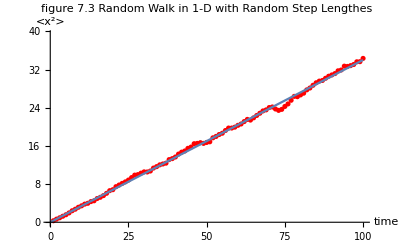

```mathematica
t=100;
n=500; (*number of walkers*)
x=Table[0,{i,n}];
x2=Table[0,{i,n}]; 
x2Ave=Table[0.0,{i,t}];
For[j=1,j≤t,j++, 
For[i=1,i≤n,i++, 
If[RandomReal[]>0.5,x[[i]]+=RandomReal[],x[[i]]-=RandomReal[]]; 
x2[[i]]=x[[i]]^2;
];
x2Ave[[j]]=Mean[x2]
];
plot=Table[{i,x2Ave[[i]]},{i,t}];
model=α*τ;
slope=α/.FindFit[plot,model,α,τ];
Show[ListPlot[plot,PlotStyle->Red],Plot[slope*x,{x,0,t}],PlotRange->{All,{0,Max[x2Ave]+5}},PlotLabel->"figure 7.3\nRandom Walk in 1-D with Random Step Length",
AxesLabel->{"time","<x^2>"}]
```

## Problem 2

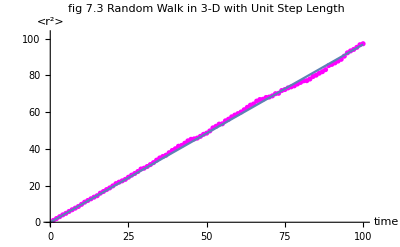

```mathematica
ClearAll["Global`*"]
t=100;
n=500; (*number of walkers*)
r=Table[{0,0,0},{i,n}];
r2=Table[0,{i,n}]; (*x^2*)
r2Ave=Table[0.0,{i,t}];
For[j=1,j≤t,j++, For[i=1,i≤n,i++, 
p=RandomReal[];If[p<1/6,r[[i,1]]++,If[p<2/6,r[[i,1]]--,If[p<3/6,r[[i,2]]++,If[p<4/6,r[[i,2]]--,If[p<5/6,r[[i,3]]++,r[[i,3]]--]]]]]; 
r2[[i]]=r[[i,1]]^2+r[[i,2]]^2+r[[i,3]]^2;
];
r2Ave[[j]]=Mean[r2]
];

plot=Table[{i,r2Ave[[i]]},{i,t}];
model=α*τ;
slope=α/.FindFit[plot,model,α,τ];

Show[ListPlot[plot,PlotStyle->Magenta],Plot[slope*x,{x,0,t}],PlotRange->{All,{0,Max[r2Ave]+5}},PlotLabel->"fig 7.3\nRandom Walk in 3-D with Unit Step Length",
AxesLabel->{"time","<r^2>"}]
```

## Problem 3

```mathematica
ClearAll["Global`*"]
dx=dy=1; x=y=Range[-10,10,dx]; dt=.25; tmax=40 dt; t=Range[0,tmax,dt]; d=1;
temp=0*t; h=0*t;
ρ=Table[0.0,{i,Length[t]},{j,Length[x]},{k,Length[y]}]; (*ρ(t,x,y)*)
midx=Flatten[Position[x,0]][[1]]; midy=Flatten[Position[y,0]][[1]]; 
For[i=midx-2,i≤midx+2,i++, For[j=midy-2,j≤midy+2,j++,ρ[[1,i,j]]=1;]]

temp[[1]]=Table[{x[[i]],y[[j]],ρ[[1,i,j]]},{i,Length[x]},{j,Length[y]}]; (*temp list*)
temp[[1]]=Flatten[temp[[1]]];
h[[1]]=Table[{temp[[1,i]],temp[[1,i+1]],temp[[1,i+2]]},{i,1,Length[temp[[1]]]-2,3}];
ListPlot3D[h[[1]],AxesLabel->{"x","y","cream density"},PlotLabel->"fig 7.11 (left)\nInitial Condition",PlotTheme->"Scientific",PlotRange->{All,All,{0,1}}]

(*applying the diffusion equation*)
Monitor[For[n=2,n≤Length[t],n++, (*on time*)For[j=2,j<Length[y],j++, (*on y*)For[i=2,i<Length[x],i++, (*on x*)ρ[[n,i,j]]=ρ[[n-1,i,j]]+1/4*(d*dt)/dx^2*(ρ[[n-1,i+1,j]]+ρ[[n-1,i-1,j]]+ρ[[n-1,i,j+1]]+ρ[[n-1,i,j-1]]-4*ρ[[n-1,i,j]]);
temp[[n]]=Table[{x[[i]],y[[j]],ρ[[n,i,j]]},{i,Length[x]},{j,Length[y]}]; (*temporary list*)
temp[[n]]=Flatten[temp[[n]]];
h[[n]]=Table[{temp[[n,i]],temp[[n,i+1]],temp[[n,i+2]]},{i,1,Length[temp[[n]]]-2,3}];]]],ProgressIndicator[n,{2,Length[t]+1}]]
ListPlot3D[h[[7]],AxesLabel->{"x","y","cream density"},PlotRange->{All,All,{0,1}},PlotLabel->"fig 7.11 (middle)\nt=6Δt",PlotTheme->"Scientific"]
ListPlot3D[h[[21]],AxesLabel->{"x","y","cream density"},PlotRange->{All,All,{0,1}},PlotLabel->"fig 7.11 (right\nt=20Δt",PlotTheme->"Scientific"]
plot=Table[ListPlot3D[h[[n]],AxesLabel->{"x","y","cream density"},PlotRange->{All,All,{0,1}},
PlotLabel->"fig 7.11 time evolution",PlotTheme->"Scientific"],{n,Length[t]}];
Manipulate[plot[[n]],{n,1,Length[t],1,AnimationRate->2}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## Problem 4

```mathematica
ClearAll["Global`*"] 
(*used x to label the vertical axis and y to label the horizontal axis*)
t=250; 
x=y=Range[-40,40]; lx=Length[x]; ly=Length[y];
midx=Flatten[Position[x,0]][[1]]; midy=Flatten[Position[y,0]][[1]]; (*seed points*)

lat=Table[0,{i,lx},{j,ly}];
lat[[midx,midy]]=1; (*initial condition*)
filled={{midx,midy}}; 
sites=Table[i+(j-1)ly,{j,1,ly},{i,1,lx}];
siteMatrix = Array[0 &,{lx + 2, ly + 2}] ;
siteMatrix[[2;;lx+1,2;;ly+1]] = sites;
siteMatrix[[1]] = siteMatrix[[lx+1]];
siteMatrix[[All,1]] = siteMatrix[[All,ly+1]];
siteMatrix[[lx+2]] = siteMatrix[[2]];
siteMatrix[[All,ly+2]] = siteMatrix[[All,2]];
nTab=Table[0,{i,lx*ly},{j,4}]; 

k = 1; (*from the Ising model code*)
Do[
nTab[[k,1]] = siteMatrix[[i,j+1]];
nTab[[k,2]] = siteMatrix[[i+1,j]];
nTab[[k,3]] = siteMatrix[[i,j-1]];
nTab[[k,4]] = siteMatrix[[i-1,j]]; k++,
{i,2,lx+1},{j,2,ly+1}];

plot=Table[0,{i,t}];
plot[[1]]=ArrayPlot[lat];

Monitor[

For[n=2,n≤t,n++,
e={}; temp={}; 

For[k=1,k<=Length[filled],k++,
nx=filled[[k,1]]; ny=filled[[k,2]]; (*positions of the filled spots in lat*)
AppendTo[temp,nTab[[sites[[nx,ny]]]]]; 

If[lat[[nx+1,ny]]==1 && lat[[nx-1,ny]]==1 && lat[[nx,ny+1]]==1 && lat[[nx,ny-1]]==1,Delete[filled,k]] 
];

temp=Flatten[temp];
temp=DeleteDuplicates[temp];
For[l=1,l<=Length[temp],l++,
If[lat[[Position[sites,temp[[l]]][[1,1]],Position[sites,temp[[l]]][[1,2]]]]==0,AppendTo[e,temp[[l]]]] 
];

pf=RandomReal[];

xf=Position[sites,e[[Ceiling[pf*Length[e]]]]][[1,1]]; yf=Position[sites,e[[Ceiling[pf*Length[e]]]]][[1,2]]; 
AppendTo[filled,{xf,yf}]; 

lat[[xf,yf]]=1;
plot[[n]]=ArrayPlot[lat]
]
,ProgressIndicator[n,{2,t+1}]];

Manipulate[plot[[n]],{n,1,t,1,AnimationRate->50}]
```